```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
RemoveBackground[imgs]
```

RemoveBackground::imginv: Expecting an image or graphics instead of ….

RemoveBackground[{-Graphics-,-Graphics-,-Graphics-}]

```mathematica
RemoveBackground[#]&/@imgs
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
res=ImageMultiply[imgs[[1]],SelectComponents[FillingTransform@Binarize[imgs[[1]]],"Area",-1]];
GraphicsRow[{imgs[[1]],res}]
```

-Graphics-

```mathematica
ImageForestingComponents[imgs[[1]]]//Colorize
```

-Graphics-

```mathematica
ClusteringComponents[imgs[[1]]]//Colorize
```

Colorize::invinput: Expecting an integer matrix or an image instead of {{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, <<672>>, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, <<957>>}.

Colorize[{1}]
 |  |  |  |

```mathematica
RemoveBackground[imgs[[1]],"Blurred"]
```

-Graphics-

```mathematica
RemoveBackground[imgs[[1]],{"Foreground","Bright"}]
```

-Graphics-

```mathematica
Module[{boundingBox},Column[{boundingBox=ImageBoundingBoxes[imgs[[1]]],HighlightImage[imgs[[1]],boundingBox]}]]
```

<|cup→{Rectangle[{90.8413,274.266},{530.222,807.469}]},cellphone→{Rectangle[{535.556,560.336},{717.221,681.743}]}|>
-Graphics-

```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{boundingBox},Column[{boundingBox=ImageBoundingBoxes[imgs[[1]]],HighlightImage[imgs[[3]],boundingBox]}]]
```

<|cup→{Rectangle[{64.8717,278.235},{684.894,800.211}]},chair→{Rectangle[{0,732.084},{163.343,923.856}],Rectangle[{626.869,833.297},{718,888.617}],Rectangle[{417.553,838.298},{543.067,902.478}]}|>
-Graphics-

-Graphics-

```mathematica
boundingBoxCoord=First[Flatten@Values[ImageBoundingBoxes[imgs[[1]]]]]
```

Rectangle[{64.8717,278.235},{684.894,800.211}]

```mathematica
trimmedImages=ImageTrim[imgs[[1]],boundingBoxCoord];
```

```mathematica
%38
```

-Graphics-

```mathematica
RemoveBackground[trimmedImages]
```

-Graphics-

```mathematica
imgs=ConformImages[ImageTrim[#,First[Flatten@Values[ImageBoundingBoxes[#]]]]&/@imgs]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
mask=Erosion[Binarize[imgs[[2]],0],1];
```

```mathematica
parallaxL=First@ImageDisplacements[imgs[[{2,1}]]];
```

```mathematica
parallaxR=First@ImageDisplacements[imgs[[{2,3}]]];
```

```mathematica
parallax=parallaxL-parallaxR;
```

```mathematica
depth=Blur@Opening[ImageMultiply[ImageAdjust@Image[parallax[[All,All,1]]],mask],DiskMatrix[4]]
```

-Graphics-

```mathematica
depthFunction=ListInterpolation[Transpose@Reverse@ImageData[depth]];
```

```mathematica
resolution=ImageAdjust@ImageSaliencyFilter[imgs[[2]]];
```

```mathematica
resolutionFunction=ListInterpolation[Transpose@Reverse@ImageData@resolution];
```

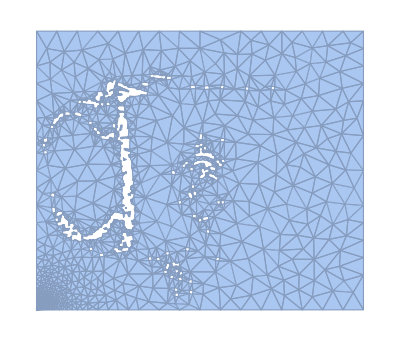

```mathematica
Ω=TriangulateMesh[ImageMesh[Erosion[mask,DiskMatrix[2]]],MeshRefinementFunction->Function[{vertices,area},area>32+512 (1-resolutionFunction@@Mean[vertices])^6]]
```

```mathematica
Graphics3D[GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]}],PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},ViewPoint->Top]
```

InterpolatingFunction::dmval: Input value {0.,546.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {640.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
texture=SetAlphaChannel[imgs[[2]],mask]
```

-Graphics-

```mathematica
Graphics3D[{Texture[texture],GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]},VertexTextureCoordinates->Map[#/ImageDimensions[texture]&,MeshCoordinates[Ω]]]},PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},Lighting->{{"Ambient",White}},ViewPoint->Top,Boxed->False]
```

InterpolatingFunction::dmval: Input value {0.,546.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {640.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-